Инициализация...

Mathematica version is 10. Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 10. Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.02.001

Release date: 2016/04/12

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.02
BerremanCommonVersion = 6.02
BerremanDirectVersion = 6.02
BerremanInverseVersion = 5.03
FieldAlgebraVersion = 6.02
FieldIOVersion = 6.02
FieldIOFormatVersion = 6.02

Copyright: K^3, 2001 - 2016.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (600 | 600 | 1 | λ | 1/1000000000
0 | 85 | 5 | ϕ | °
0 | 0 | 45 | β | °
-1 | 1 | 0.5 | e | )

---------------------------------------------

Оптические параметры первого тонкого слоя.

epsLayer1 = (2.25 | 0 | 0
0 | 4. | 0
0 | 0 | 3.0625)

Оптические параметры нижней среды...

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,1.5,{0,0,30,γ,°},{{0,{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},Layered System,1,0,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25,0,0},{0,2.25,0},{0,0,2.25}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},{{600,600,1,λ,1/1000000000},{0,85,5,ϕ,°},{0,0,45,β,°},{0,0,30,γ,°},{-1,1,0.5,e},{0,0,1,φ_1,°},{0,0,1,θ_1,°},{0,0,1,ψ_1,°},{0,0,30,φ_1,°},{0,0,30,θ_1,°},{0,0,30,ψ_1,°},{75,75,10,h,1/1000000000}},{UseThickLastLayer→False}}}

==============================================

Производим вычисления для различных значений параметров....

PerformAllCalculations::Calculating...

Start time: 0:38:47

Total number of points to calculate: 90

Estimated total calculation time: 0:00:01

Estimated end time: 0:38:49

==============================================

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
One Layer biaxial thin film between two semi-infinite media. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film between TWO SEMI-INFINITE isotropic media; nOut is IGNORED !!! |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | 1.5 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | 2.25 | 0 | 0 |  | 0 | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 2.25 | 0 |  | 0 | 0 | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 0 | 2.25 |  | 0 | 0 | 0 |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1.5 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 2. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 0. | 1.75 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 2.25 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 4. | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 3.0625 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ_1 | θ_1 | ψ_1 | φ_1 | θ_1 | ψ_1 | h | Output | S_(R,0) | S_(R,1) | S_(R,2) | S_(R,3) | R | T | γ_R | ° γ_R | χ_R | ° χ_R | p_R | χ_r | e_r | ψ_pp | Δ_pp | R_p | R_s | T_p | T_s
 | 1. | 600. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123306 | -0.0833058 | 0. | 0.0909091 | 0.123306 | 0.876694 | 0.414507 | 23.7495 | 0.785398 | 45. | 1. | -90. | 0.44 | 23.7495 | -180. | 0.02 | 0.103306 | 0.48 | 0.396694
 | 2. | 600. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0733223 | -0.00932231 | 0. | 0.0727273 | 0.0733223 | 0.926678 | 0.721655 | 41.3478 | 0.785398 | 45. | 1. | -90. | 0.88 | 23.7495 | -180. | 0.032 | 0.0413223 | 0.768 | 0.158678
 | 3. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.04 | 0.04 | 0. | 0. | 0.04 | 0.96 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 23.7495 | -180. | 0.04 | 0. | 0.96 | 0.
 | 4. | 600. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0733223 | -0.00932231 | 0. | -0.0727273 | 0.0733223 | 0.926678 | -0.721655 | -41.3478 | -0.785398 | -45. | 1. | 90. | -0.88 | 23.7495 | -180. | 0.032 | 0.0413223 | 0.768 | 0.158678
 | 5. | 600. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123306 | -0.0833058 | 0. | -0.0909091 | 0.123306 | 0.876694 | -0.414507 | -23.7495 | -0.785398 | -45. | 1. | 90. | -0.44 | 23.7495 | -180. | 0.02 | 0.103306 | 0.48 | 0.396694
 | 6. | 600. | 5. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123679 | -0.084232 | 0.000138407 | 0.0905624 | 0.123679 | 0.876321 | 0.410799 | 23.537 | 0.784634 | 44.9562 | 1. | 89.9529 | 0.435581 | 23.5371 | 179.957 | 0.0197237 | 0.103956 | 0.480276 | 0.396044
 | 7. | 600. | 5. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0731402 | -0.0100244 | 0.000110725 | 0.0724499 | 0.0731402 | 0.92686 | 0.716649 | 41.061 | 0.784634 | 44.9562 | 1. | 89.6836 | 0.871157 | 23.5371 | 179.957 | 0.0315579 | 0.0415823 | 0.768442 | 0.158418
 | 8. | 600. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0394474 | 0.0394474 | 0. | 0. | 0.0394474 | 0.960553 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 23.5371 | 179.957 | 0.0394474 | 0. | 0.960553 | 0.
 | 9. | 600. | 5. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0731402 | -0.0100244 | -0.000110725 | -0.0724499 | 0.0731402 | 0.92686 | -0.716649 | -41.061 | -0.786162 | -45.0438 | 1. | -89.6836 | -0.871157 | 23.5371 | 179.957 | 0.0315579 | 0.0415823 | 0.768442 | 0.158418
 | 10. | 600. | 5. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123679 | -0.084232 | -0.000138407 | -0.0905624 | 0.123679 | 0.876321 | -0.410799 | -23.537 | -0.786162 | -45.0438 | 1. | -89.9529 | -0.435581 | 23.5371 | 179.957 | 0.0197237 | 0.103956 | 0.480276 | 0.396044
 | 11. | 600. | 10. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.124823 | -0.0870244 | 0.000552797 | 0.0894827 | 0.124823 | 0.875177 | 0.399657 | 22.8987 | 0.782309 | 44.823 | 1. | 89.818 | 0.422389 | 22.8992 | 179.828 | 0.0188991 | 0.105924 | 0.481101 | 0.394076
 | 12. | 600. | 10. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.072608 | -0.0121308 | 0.000442237 | 0.0715861 | 0.072608 | 0.927392 | 0.701412 | 40.188 | 0.782309 | 44.823 | 1. | 88.9561 | 0.844705 | 22.8992 | 179.828 | 0.0302386 | 0.0423694 | 0.769761 | 0.157631
 | 13. | 600. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0377983 | 0.0377983 | 0. | 0. | 0.0377983 | 0.962202 | 0. | 0. | 0. | 0. | 1. | 8.53774×10^-7 | 0. | 22.8992 | 179.828 | 0.0377983 | 0. | 0.962202 | 0.
 | 14. | 600. | 10. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.072608 | -0.0121308 | -0.000442237 | -0.0715861 | 0.072608 | 0.927392 | -0.701412 | -40.188 | -0.788487 | -45.177 | 1. | -88.9561 | -0.844705 | 22.8992 | 179.828 | 0.0302386 | 0.0423694 | 0.769761 | 0.157631
 | 15. | 600. | 10. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.124823 | -0.0870244 | -0.000552797 | -0.0894827 | 0.124823 | 0.875177 | -0.399657 | -22.8987 | -0.788487 | -45.177 | 1. | -89.818 | -0.422389 | 22.8992 | 179.828 | 0.0188991 | 0.105924 | 0.481101 | 0.394076
 | 16. | 600. | 15. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126804 | -0.0917229 | 0.0012403 | 0.0875482 | 0.126804 | 0.873196 | 0.381035 | 21.8317 | 0.778315 | 44.5942 | 1. | 89.6126 | 0.400613 | 21.8344 | 179.622 | 0.0175407 | 0.109264 | 0.482459 | 0.390736
 | 17. | 600. | 15. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0717705 | -0.0156403 | 0.000992237 | 0.0700386 | 0.0717705 | 0.928229 | 0.675332 | 38.6937 | 0.778315 | 44.5942 | 1. | 88.185 | 0.800969 | 21.8344 | 179.622 | 0.0280651 | 0.0437054 | 0.771935 | 0.156295
 | 18. | 600. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0350814 | 0.0350814 | 0. | 0. | 0.0350814 | 0.964919 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 21.8344 | 179.622 | 0.0350814 | 0. | 0.964919 | 0.
 | 19. | 600. | 15. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0717705 | -0.0156403 | -0.000992237 | -0.0700386 | 0.0717705 | 0.928229 | -0.675332 | -38.6937 | -0.792481 | -45.4058 | 1. | -88.185 | -0.800969 | 21.8344 | 179.622 | 0.0280651 | 0.0437054 | 0.771935 | 0.156295
 | 20. | 600. | 15. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126804 | -0.0917229 | -0.0012403 | -0.0875482 | 0.126804 | 0.873196 | -0.381035 | -21.8317 | -0.792481 | -45.4058 | 1. | -89.6126 | -0.400613 | 21.8344 | 179.622 | 0.0175407 | 0.109264 | 0.482459 | 0.390736
 | 21. | 600. | 20. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.129744 | -0.0983915 | 0.00219484 | 0.0845452 | 0.129744 | 0.870256 | 0.354865 | 20.3323 | 0.772421 | 44.2565 | 1. | 89.3611 | 0.370552 | 20.3406 | 179.349 | 0.0156764 | 0.114068 | 0.484324 | 0.385932
 | 22. | 600. | 20. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0707095 | -0.0205449 | 0.00175587 | 0.0676362 | 0.0707095 | 0.929291 | 0.637442 | 36.5227 | 0.772421 | 44.2565 | 1. | 87.5575 | 0.740575 | 20.3406 | 179.349 | 0.0250823 | 0.0456272 | 0.774918 | 0.154373
 | 23. | 600. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0313529 | 0.0313529 | 0. | 0. | 0.0313529 | 0.968647 | 0. | 0. | 0. | 0. | 1. | 1.20742×10^-6 | 0. | 20.3406 | 179.349 | 0.0313529 | 0. | 0.968647 | 0.
 | 24. | 600. | 20. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0707095 | -0.0205449 | -0.00175587 | -0.0676362 | 0.0707095 | 0.929291 | -0.637442 | -36.5227 | -0.798376 | -45.7435 | 1. | -87.5575 | -0.740575 | 20.3406 | 179.349 | 0.0250823 | 0.0456272 | 0.774918 | 0.154373
 | 25. | 600. | 20. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.129744 | -0.0983915 | -0.00219484 | -0.0845452 | 0.129744 | 0.870256 | -0.354865 | -20.3323 | -0.798376 | -45.7435 | 1. | -89.3611 | -0.370552 | 20.3406 | 179.349 | 0.0156764 | 0.114068 | 0.484324 | 0.385932
 | 26. | 600. | 25. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.133824 | -0.107113 | 0.00340533 | 0.0801505 | 0.133824 | 0.866176 | 0.321078 | 18.3964 | 0.764168 | 43.7836 | 1. | 89.0895 | 0.332586 | 18.4158 | 179.023 | 0.0133555 | 0.120469 | 0.486644 | 0.379531
 | 27. | 600. | 25. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0695563 | -0.0268186 | 0.00272426 | 0.0641204 | 0.0695563 | 0.930444 | 0.586411 | 33.5989 | 0.764168 | 43.7836 | 1. | 87.0999 | 0.664371 | 18.4158 | 179.023 | 0.0213689 | 0.0481875 | 0.778631 | 0.151813
 | 28. | 600. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0267111 | 0.0267111 | 0. | 0. | 0.0267111 | 0.973289 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 18.4158 | 179.023 | 0.0267111 | 0. | 0.973289 | 0.
 | 29. | 600. | 25. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0695563 | -0.0268186 | -0.00272426 | -0.0641204 | 0.0695563 | 0.930444 | -0.586411 | -33.5989 | -0.806629 | -46.2164 | 1. | -87.0999 | -0.664371 | 18.4158 | 179.023 | 0.0213689 | 0.0481875 | 0.778631 | 0.151813
 | 30. | 600. | 25. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.133824 | -0.107113 | -0.00340533 | -0.0801505 | 0.133824 | 0.866176 | -0.321078 | -18.3964 | -0.806629 | -46.2164 | 1. | -89.0895 | -0.332586 | 18.4158 | 179.023 | 0.0133555 | 0.120469 | 0.486644 | 0.379531
 | 31. | 600. | 30. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.139301 | -0.11798 | 0.00485315 | 0.0739042 | 0.139301 | 0.860699 | 0.279617 | 16.0208 | 0.752611 | 43.1214 | 1. | 88.8222 | 0.287139 | 16.0595 | 178.665 | 0.0106603 | 0.128641 | 0.48934 | 0.371359
 | 32. | 600. | 30. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0685127 | -0.0343998 | 0.00388252 | 0.0591234 | 0.0685127 | 0.931487 | 0.520544 | 29.825 | 0.752611 | 43.1214 | 1. | 86.7803 | 0.573284 | 16.0595 | 178.665 | 0.0170565 | 0.0514563 | 0.782944 | 0.148544
 | 33. | 600. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0213206 | 0.0213206 | 0. | 0. | 0.0213206 | 0.978679 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 16.0595 | 178.665 | 0.0213206 | 0. | 0.978679 | 0.
 | 34. | 600. | 30. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0685127 | -0.0343998 | -0.00388252 | -0.0591234 | 0.0685127 | 0.931487 | -0.520544 | -29.825 | -0.818185 | -46.8786 | 1. | -86.7803 | -0.573284 | 16.0595 | 178.665 | 0.0170565 | 0.0514563 | 0.782944 | 0.148544
 | 35. | 600. | 30. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.139301 | -0.11798 | -0.00485315 | -0.0739042 | 0.139301 | 0.860699 | -0.279617 | -16.0208 | -0.818185 | -46.8786 | 1. | -88.8222 | -0.287139 | 16.0595 | 178.665 | 0.0106603 | 0.128641 | 0.48934 | 0.371359
 | 36. | 600. | 35. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.146531 | -0.131079 | 0.00650928 | 0.0651698 | 0.146531 | 0.853469 | 0.230449 | 13.2037 | 0.735622 | 42.1481 | 1. | 88.5785 | 0.234617 | 13.2746 | 178.297 | 0.00772571 | 0.138805 | 0.492274 | 0.361195
 | 37. | 600. | 35. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0678831 | -0.0431608 | 0.00520742 | 0.0521358 | 0.0678831 | 0.932117 | 0.437874 | 25.0884 | 0.735622 | 42.1481 | 1. | 86.5602 | 0.468186 | 13.2746 | 178.297 | 0.0123611 | 0.055522 | 0.787639 | 0.144478
 | 38. | 600. | 35. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0154514 | 0.0154514 | 0. | 0. | 0.0154514 | 0.984549 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 13.2746 | 178.297 | 0.0154514 | 0. | 0.984549 | 0.
 | 39. | 600. | 35. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0678831 | -0.0431608 | -0.00520742 | -0.0521358 | 0.0678831 | 0.932117 | -0.437874 | -25.0884 | -0.835174 | -47.8519 | 1. | -86.5602 | -0.468186 | 13.2746 | 178.297 | 0.0123611 | 0.055522 | 0.787639 | 0.144478
 | 40. | 600. | 35. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.146531 | -0.131079 | -0.00650928 | -0.0651698 | 0.146531 | 0.853469 | -0.230449 | -13.2037 | -0.835174 | -47.8519 | 1. | -88.5785 | -0.234617 | 13.2746 | 178.297 | 0.00772571 | 0.138805 | 0.492274 | 0.361195
 | 41. | 600. | 40. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.156004 | -0.146461 | 0.00833113 | 0.0530755 | 0.156004 | 0.843996 | 0.173575 | 9.94511 | 0.70755 | 40.5396 | 1. | 88.3722 | 0.175339 | 10.0721 | 177.945 | 0.00477149 | 0.151233 | 0.495229 | 0.348767
 | 42. | 600. | 40. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681274 | -0.0528586 | 0.00666491 | 0.0424604 | 0.0681274 | 0.931873 | 0.336446 | 19.2769 | 0.70755 | 40.5396 | 1. | 86.4068 | 0.349743 | 10.0721 | 177.945 | 0.00763439 | 0.060493 | 0.792366 | 0.139507
 | 43. | 600. | 40. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00954299 | 0.00954299 | 0. | 0. | 0.00954299 | 0.990457 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 10.0721 | 177.945 | 0.00954299 | 0. | 0.990457 | 0.
 | 44. | 600. | 40. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681274 | -0.0528586 | -0.00666491 | -0.0424604 | 0.0681274 | 0.931873 | -0.336446 | -19.2769 | -0.863247 | -49.4604 | 1. | -86.4068 | -0.349743 | 10.0721 | 177.945 | 0.00763439 | 0.060493 | 0.792366 | 0.139507
 | 45. | 600. | 40. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.156004 | -0.146461 | -0.00833113 | -0.0530755 | 0.156004 | 0.843996 | -0.173575 | -9.94511 | -0.863247 | -49.4604 | 1. | -88.3722 | -0.175339 | 10.0721 | 177.945 | 0.00477149 | 0.151233 | 0.495229 | 0.348767
 | 46. | 600. | 45. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.168402 | -0.164094 | 0.0102595 | 0.036431 | 0.168402 | 0.831598 | 0.109029 | 6.24689 | 0.648145 | 37.136 | 1. | 88.2112 | 0.109463 | 6.49404 | 177.637 | 0.00215413 | 0.166248 | 0.497846 | 0.333752
 | 47. | 600. | 45. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0699457 | -0.0630525 | 0.00820763 | 0.0291448 | 0.0699457 | 0.930054 | 0.214893 | 12.3125 | 0.648145 | 37.136 | 1. | 86.2917 | 0.218264 | 6.49404 | 177.637 | 0.0034466 | 0.0664991 | 0.796553 | 0.133501
 | 48. | 600. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00430825 | 0.00430825 | 0. | 0. | 0.00430825 | 0.995692 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 6.49404 | 177.637 | 0.00430825 | 0. | 0.995692 | 0.
 | 49. | 600. | 45. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0699457 | -0.0630525 | -0.00820763 | -0.0291448 | 0.0699457 | 0.930054 | -0.214893 | -12.3125 | -0.922651 | -52.864 | 1. | -86.2917 | -0.218264 | 6.49404 | 177.637 | 0.0034466 | 0.0664991 | 0.796553 | 0.133501
 | 50. | 600. | 45. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.168402 | -0.164094 | -0.0102595 | -0.036431 | 0.168402 | 0.831598 | -0.109029 | -6.24689 | -0.922651 | -52.864 | 1. | -88.2112 | -0.109463 | 6.49404 | 177.637 | 0.00215413 | 0.166248 | 0.497846 | 0.333752
 | 51. | 600. | 50. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.184686 | -0.183778 | 0.012216 | 0.0136056 | 0.184686 | 0.815314 | 0.0368678 | 2.11237 | 0.419581 | 24.0402 | 1. | 88.0985 | 0.0368845 | 2.84097 | 177.402 | 0.000453696 | 0.184232 | 0.499546 | 0.315768
 | 52. | 600. | 50. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0744187 | -0.0729669 | 0.00977278 | 0.0108844 | 0.0744187 | 0.925581 | 0.0733931 | 4.20511 | 0.419581 | 24.0402 | 1. | 86.1858 | 0.0735251 | 2.84097 | 177.402 | 0.000725914 | 0.0736928 | 0.799274 | 0.126307
 | 53. | 600. | 50. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.000907392 | 0.000907392 | 0. | 0. | 0.000907392 | 0.999093 | 0. | 0. | 0. | 0. | 1. | 1.20742×10^-6 | 0. | 2.84097 | 177.402 | 0.000907392 | 0. | 0.999093 | 0.
 | 54. | 600. | 50. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0744187 | -0.0729669 | -0.00977278 | -0.0108844 | 0.0744187 | 0.925581 | -0.0733931 | -4.20511 | -1.15122 | -65.9598 | 1. | -86.1858 | -0.0735251 | 2.84097 | 177.402 | 0.000725914 | 0.0736928 | 0.799274 | 0.126307
 | 55. | 600. | 50. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.184686 | -0.183778 | -0.012216 | -0.0136056 | 0.184686 | 0.815314 | -0.0368678 | -2.11237 | -1.15122 | -65.9598 | 1. | -88.0985 | -0.0368845 | 2.84097 | 177.402 | 0.000453696 | 0.184232 | 0.499546 | 0.315768
 | 56. | 600. | 55. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.206245 | -0.205004 | 0.0140998 | -0.0176469 | 0.206245 | 0.793755 | -0.0428337 | -2.45419 | -0.448334 | -25.6876 | 1. | 88.0327 | -0.04286 | 3.14383 | 177.268 | 0.000620326 | 0.205625 | 0.49938 | 0.294375
 | 57. | 600. | 55. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0832423 | -0.0812573 | 0.0112798 | -0.0141175 | 0.0832423 | 0.916758 | -0.0852094 | -4.88214 | -0.448334 | -25.6876 | 1. | 86.0485 | -0.0854163 | 3.14383 | 177.268 | 0.000992521 | 0.0822498 | 0.799007 | 0.11775
 | 58. | 600. | 55. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00124065 | 0.00124065 | 0. | 0. | 0.00124065 | 0.998759 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 3.14383 | 177.268 | 0.00124065 | 0. | 0.998759 | 0.
 | 59. | 600. | 55. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0832423 | -0.0812573 | -0.0112798 | 0.0141175 | 0.0832423 | 0.916758 | 0.0852094 | 4.88214 | 1.12246 | 64.3124 | 1. | -86.0485 | 0.0854163 | 3.14383 | 177.268 | 0.000992521 | 0.0822498 | 0.799007 | 0.11775
 | 60. | 600. | 55. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.206245 | -0.205004 | -0.0140998 | 0.0176469 | 0.206245 | 0.793755 | 0.0428337 | 2.45419 | 1.12246 | 64.3124 | 1. | -88.0327 | 0.04286 | 3.14383 | 177.268 | 0.000620326 | 0.205625 | 0.49938 | 0.294375
 | 61. | 600. | 60. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.23515 | -0.2267 | 0.0157839 | -0.0604448 | 0.23515 | 0.76485 | -0.129983 | -7.44749 | -0.657686 | -37.6826 | 1. | 88.0086 | -0.13072 | 7.70331 | 177.258 | 0.00422508 | 0.230925 | 0.495775 | 0.269075
 | 62. | 600. | 60. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.09913 | -0.0856097 | 0.0126271 | -0.0483558 | 0.09913 | 0.90087 | -0.254785 | -14.5981 | -0.657686 | -37.6826 | 1. | 85.8048 | -0.260445 | 7.70331 | 177.258 | 0.00676013 | 0.0923698 | 0.79324 | 0.10763
 | 63. | 600. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00845017 | 0.00845017 | 0. | 0. | 0.00845017 | 0.99155 | 0. | 0. | 0. | 0. | 1. | 8.53774×10^-7 | 0. | 7.70331 | 177.258 | 0.00845017 | 0. | 0.99155 | 0.
 | 64. | 600. | 60. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.09913 | -0.0856097 | -0.0126271 | 0.0483558 | 0.09913 | 0.90087 | 0.254785 | 14.5981 | 0.913111 | 52.3174 | 1. | -85.8048 | 0.260445 | 7.70331 | 177.258 | 0.00676013 | 0.0923698 | 0.79324 | 0.10763
 | 65. | 600. | 60. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.23515 | -0.2267 | -0.0157839 | 0.0604448 | 0.23515 | 0.76485 | 0.129983 | 7.44749 | 0.913111 | 52.3174 | 1. | -88.0086 | 0.13072 | 7.70331 | 177.258 | 0.00422508 | 0.230925 | 0.495775 | 0.269075
 | 66. | 600. | 65. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.274587 | -0.246793 | 0.0171034 | -0.119159 | 0.274587 | 0.725413 | -0.224439 | -12.8594 | -0.714118 | -40.9159 | 1. | 88.0178 | -0.228286 | 13.001 | 177.391 | 0.0138971 | 0.26069 | 0.486103 | 0.23931
 | 67. | 600. | 65. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126511 | -0.0820408 | 0.0136828 | -0.095327 | 0.126511 | 0.873489 | -0.426689 | -24.4475 | -0.714118 | -40.9159 | 1. | 85.2657 | -0.454619 | 13.001 | 177.391 | 0.0222353 | 0.104276 | 0.777765 | 0.0957239
 | 68. | 600. | 65. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0277942 | 0.0277942 | 0. | 0. | 0.0277942 | 0.972206 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 13.001 | 177.391 | 0.0277942 | 0. | 0.972206 | 0.
 | 69. | 600. | 65. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126511 | -0.0820408 | -0.0136828 | 0.095327 | 0.126511 | 0.873489 | 0.426689 | 24.4475 | 0.856679 | 49.0841 | 1. | -85.2657 | 0.454619 | 13.001 | 177.391 | 0.0222353 | 0.104276 | 0.777765 | 0.0957239
 | 70. | 600. | 65. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.274587 | -0.246793 | -0.0171034 | 0.119159 | 0.274587 | 0.725413 | 0.224439 | 12.8594 | 0.856679 | 49.0841 | 1. | -88.0178 | 0.228286 | 13.001 | 177.391 | 0.0138971 | 0.26069 | 0.486103 | 0.23931
 | 71. | 600. | 70. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.329637 | -0.261438 | 0.0178269 | -0.199983 | 0.329637 | 0.670363 | -0.325936 | -18.6748 | -0.740945 | -42.453 | 1. | 88.0496 | -0.337991 | 18.7616 | 177.674 | 0.0340997 | 0.295538 | 0.4659 | 0.204462
 | 72. | 600. | 70. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.172775 | -0.0636555 | 0.0142615 | -0.159986 | 0.172775 | 0.827225 | -0.591816 | -33.9086 | -0.740945 | -42.453 | 1. | 83.6859 | -0.672189 | 18.7616 | 177.674 | 0.0545596 | 0.118215 | 0.74544 | 0.0817849
 | 73. | 600. | 70. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681995 | 0.0681995 | 0. | 0. | 0.0681995 | 0.931801 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 18.7616 | 177.674 | 0.0681995 | 0. | 0.931801 | 0.
 | 74. | 600. | 70. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.172775 | -0.0636555 | -0.0142615 | 0.159986 | 0.172775 | 0.827225 | 0.591816 | 33.9086 | 0.829852 | 47.547 | 1. | -83.6859 | 0.672189 | 18.7616 | 177.674 | 0.0545596 | 0.118215 | 0.74544 | 0.0817849
 | 75. | 600. | 70. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.329637 | -0.261438 | -0.0178269 | 0.199983 | 0.329637 | 0.670363 | 0.325936 | 18.6748 | 0.829852 | 47.547 | 1. | -88.0496 | 0.337991 | 18.7616 | 177.674 | 0.0340997 | 0.295538 | 0.4659 | 0.204462
 | 76. | 600. | 75. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.408684 | -0.263596 | 0.0175824 | -0.311817 | 0.408684 | 0.591316 | -0.433955 | -24.8638 | -0.757235 | -43.3863 | 1. | 88.092 | -0.463417 | 24.9176 | 178.101 | 0.0725436 | 0.33614 | 0.427456 | 0.16386
 | 77. | 600. | 75. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.250526 | -0.0183862 | 0.0140659 | -0.249454 | 0.250526 | 0.749474 | -0.73913 | -42.349 | -0.757235 | -43.3863 | 1. | 71.2916 | -0.911496 | 24.9176 | 178.101 | 0.11607 | 0.134456 | 0.68393 | 0.065544
 | 78. | 600. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.145087 | 0.145087 | 0. | 0. | 0.145087 | 0.854913 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 24.9176 | 178.101 | 0.145087 | 0. | 0.854913 | 0.
 | 79. | 600. | 75. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.250526 | -0.0183862 | -0.0140659 | 0.249454 | 0.250526 | 0.749474 | 0.73913 | 42.349 | 0.813562 | 46.6137 | 1. | -71.2916 | 0.911496 | 24.9176 | 178.101 | 0.11607 | 0.134456 | 0.68393 | 0.065544
 | 80. | 600. | 75. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.408684 | -0.263596 | -0.0175824 | 0.311817 | 0.408684 | 0.591316 | 0.433955 | 24.8638 | 0.813562 | 46.6137 | 1. | -88.092 | 0.463417 | 24.9176 | 178.101 | 0.0725436 | 0.33614 | 0.427456 | 0.16386
 | 81. | 600. | 80. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.526069 | -0.240381 | 0.0156885 | -0.467675 | 0.526069 | 0.473931 | -0.547576 | -31.3738 | -0.768632 | -44.0393 | 1. | 88.1329 | -0.609775 | 31.4051 | 178.655 | 0.142844 | 0.383225 | 0.357156 | 0.116775
 | 82. | 600. | 80. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.381841 | 0.0752602 | 0.0125508 | -0.37414 | 0.381841 | 0.618159 | -0.684811 | -39.2368 | -0.768632 | -44.0393 | 1. | 4.73391 | -0.816649 | 31.4051 | 178.655 | 0.22855 | 0.15329 | 0.57145 | 0.0467098
 | 83. | 600. | 80. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.285688 | 0.285688 | 0. | 0. | 0.285688 | 0.714312 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 31.4051 | 178.655 | 0.285688 | 0. | 0.714312 | 0.
 | 84. | 600. | 80. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.381841 | 0.0752602 | -0.0125508 | 0.37414 | 0.381841 | 0.618159 | 0.684811 | 39.2368 | 0.802165 | 45.9607 | 1. | -4.73391 | 0.816649 | 31.4051 | 178.655 | 0.22855 | 0.15329 | 0.57145 | 0.0467098
 | 85. | 600. | 80. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.526069 | -0.240381 | -0.0156885 | 0.467675 | 0.526069 | 0.473931 | 0.547576 | 31.3738 | 0.802165 | 45.9607 | 1. | -88.1329 | 0.609775 | 31.4051 | 178.655 | 0.142844 | 0.383225 | 0.357156 | 0.116775
 | 86. | 600. | 85. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707318 | -0.167828 | 0.010781 | -0.687034 | 0.707318 | 0.292682 | -0.665367 | -38.1227 | -0.777553 | -44.5505 | 1. | 88.1622 | -0.784741 | 38.1371 | 179.303 | 0.269745 | 0.437573 | 0.230255 | 0.0624269
 | 87. | 600. | 85. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.606621 | 0.256563 | 0.0086248 | -0.549627 | 0.606621 | 0.393379 | -0.566924 | -32.4824 | -0.777553 | -44.5505 | 1. | 0.962687 | -0.636638 | 38.1371 | 179.303 | 0.431592 | 0.175029 | 0.368408 | 0.0249708
 | 88. | 600. | 85. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.53949 | 0.53949 | 0. | 0. | 0.53949 | 0.46051 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 38.1371 | 179.303 | 0.53949 | 0. | 0.46051 | 0.
 | 89. | 600. | 85. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.606621 | 0.256563 | -0.0086248 | 0.549627 | 0.606621 | 0.393379 | 0.566924 | 32.4824 | 0.793244 | 45.4495 | 1. | -0.962687 | 0.636638 | 38.1371 | 179.303 | 0.431592 | 0.175029 | 0.368408 | 0.0249708
 | 90. | 600. | 85. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707318 | -0.167828 | -0.010781 | 0.687034 | 0.707318 | 0.292682 | 0.665367 | 38.1227 | 0.793244 | 45.4495 | 1. | -88.1622 | 0.784741 | 38.1371 | 179.303 | 0.269745 | 0.437573 | 0.230255 | 0.0624269)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Wed 13 Apr 2016 00:38:58, time used: 11.073, total time used: 11.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

γ of Stokes Vector R.

-Graphics3D-

==============================================

γ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

χ of Stokes Vector R.

-Graphics3D-

==============================================

χ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

p of Stokes Vector R.

-Graphics3D-

==============================================

Azimuth of Reflected light in Degrees (new).

-Graphics3D-

==============================================

Ellipticity of Reflected light (new).

-Graphics3D-

==============================================

Psi pp in degrees.

-Graphics3D-

==============================================

Delta pp in degrees.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Stokes Vector R.

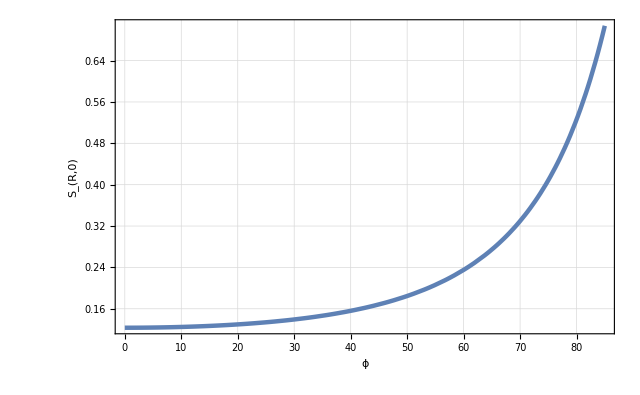

Stokes Vector R.

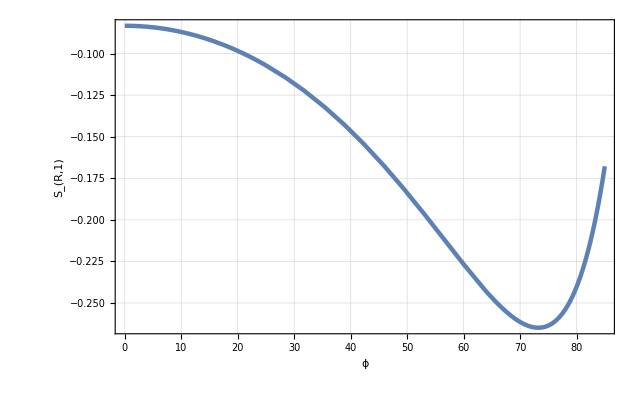

Stokes Vector R.

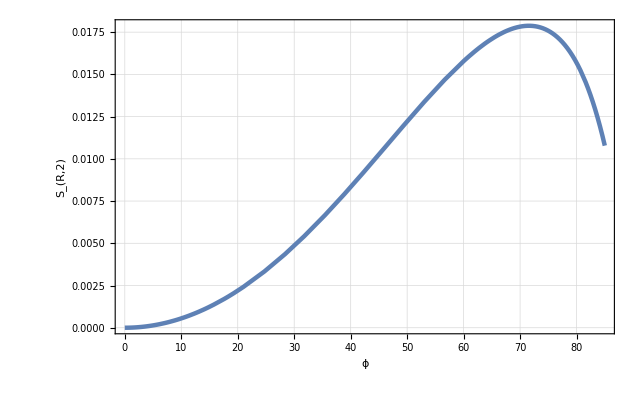

Stokes Vector R.

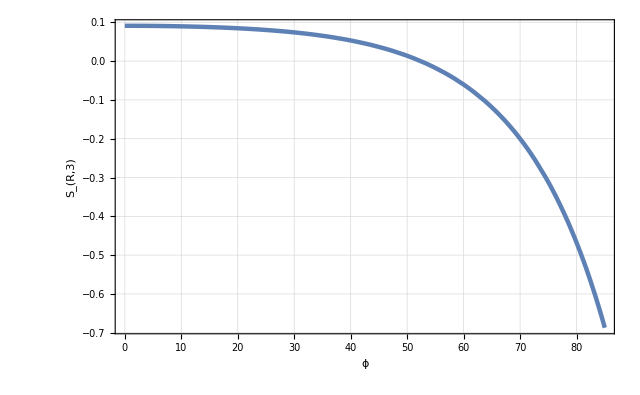

Full intensity of Reflected light.

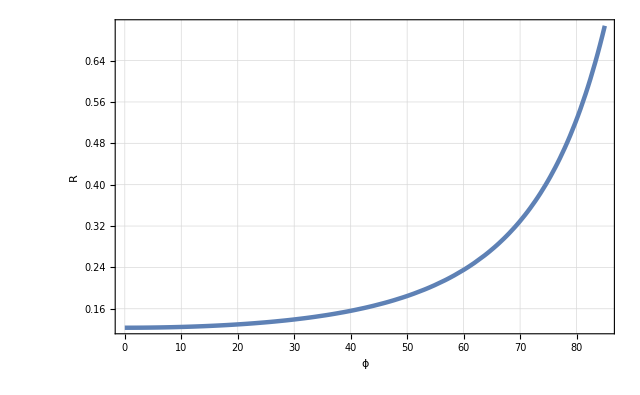

Full intensity of Transmitted light.

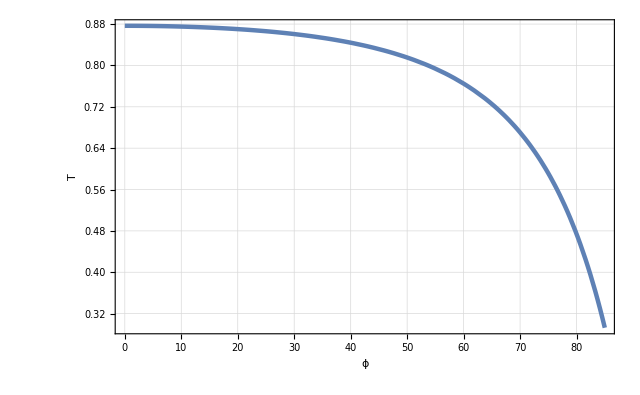

γ of Stokes Vector R.

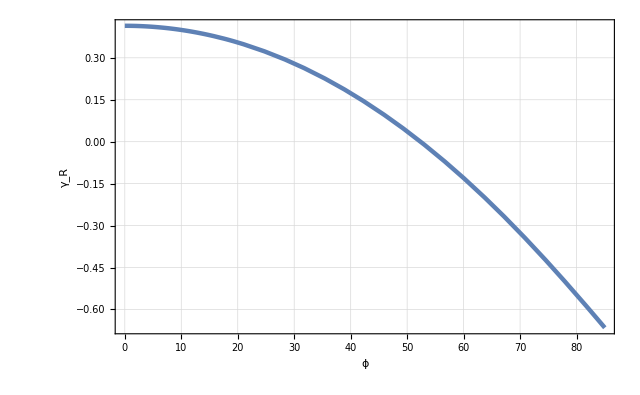

γ of Stokes Vector R (in degrees).

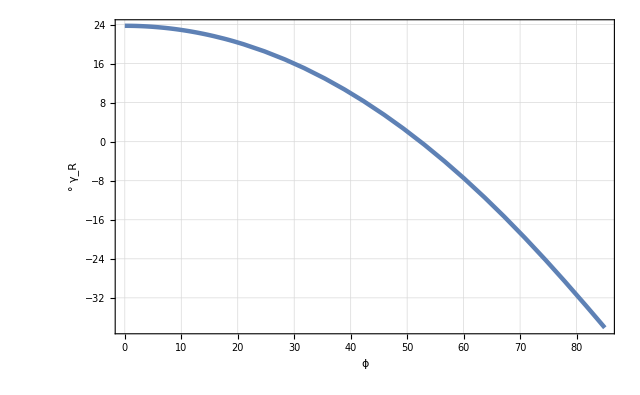

χ of Stokes Vector R.

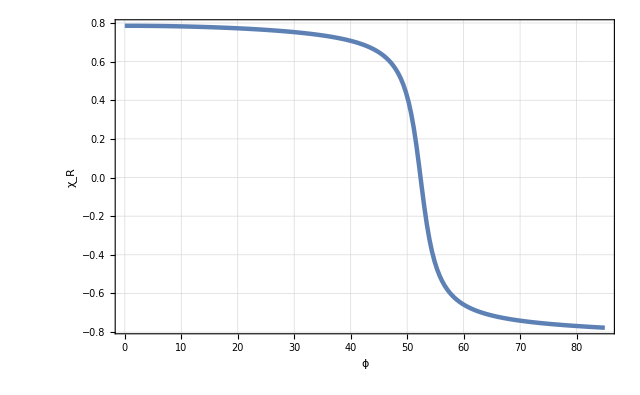

χ of Stokes Vector R (in degrees).

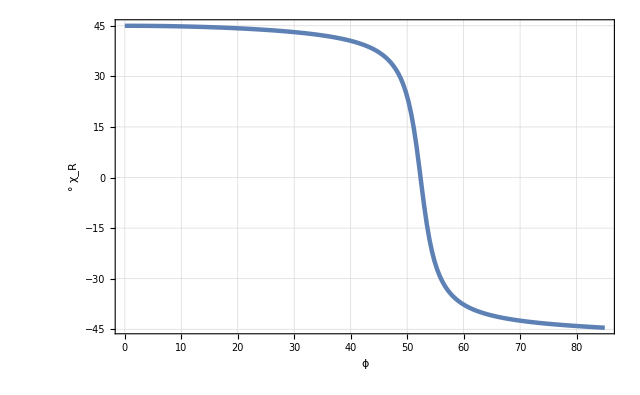

p of Stokes Vector R.

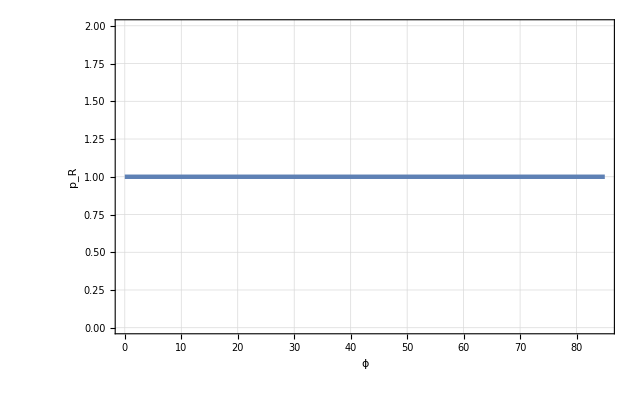

Azimuth of Reflected light in Degrees (new).

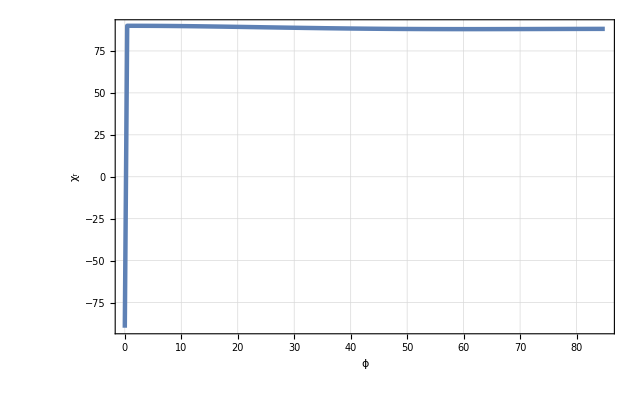

Ellipticity of Reflected light (new).

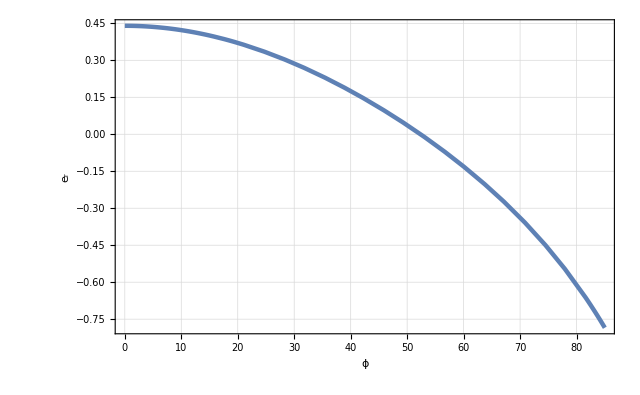

Psi pp in degrees.

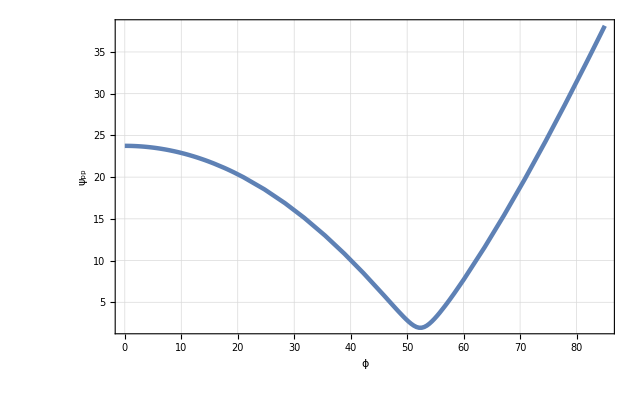

Delta pp in degrees.

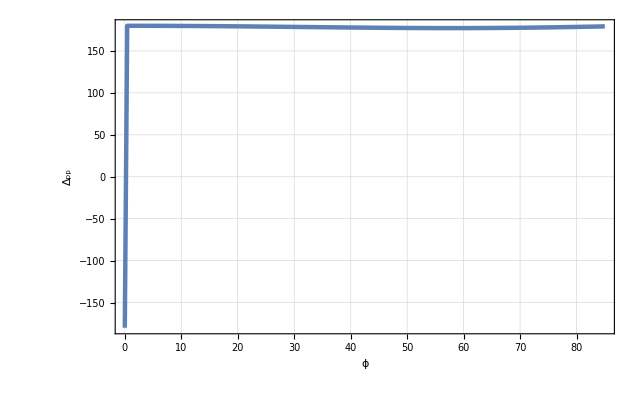

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

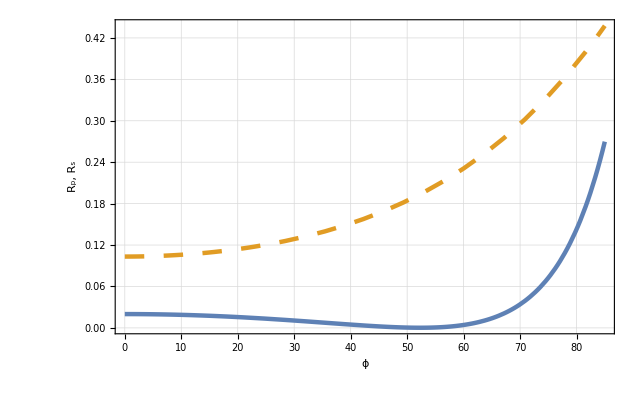

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

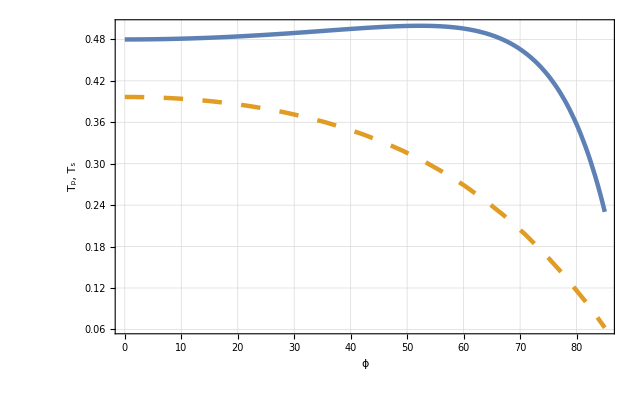

Wed 13 Apr 2016 00:41:54, time used: 177, total time used: 188.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
PathList={"W:\\Math\\BM\\"};
BaseDir="W:\\Math\\BM\\";
BaseFileName="Example_06";
OutDir=BaseDir<>"Calc\\";
(* ============================================== *)
useParallelTbl=False;
Get["BerremanInit.m",Path-> PathList];
Initialize[PathList, useParallelTbl];
(* ============================================== *)
opts={BDPlotFigures -> True,UseEulerAngles->False};
(* ============================================== *)
(*
FuncList={{StokesVectorI[1],StokesVectorI[2],StokesVectorI[3],StokesVectorI[4]},{StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4]},{EltEG[1],EltEG[2],EltEG[3],EltEG[4]},{XitEGDegree[1],XitEGDegree[2],XitEGDegree[3],XitEGDegree[4]},{IFull,RFull,TFull},{Ix,Iy,Rx,Ry,Tx,Ty},{Eli,Elr,Elt},{XiiDegree, XirDegree,XitDegree},{Sin2Xii,Sin2Xir,Sin2Xit}};
*)

FuncList={StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4],RFull,TFull, StokesGammaR, StokesGammaDegreeR,StokesChiR, StokesChiDegreeR, StokesPolarizedR,XirDegree,Elr,PsiPPDegree,DeltaPPDegree,{Rx,Ry},{Tx,Ty}};

(* ============================================== *)
systemDescription="One Layer biaxial thin film between two semi-infinite media.";
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper=1; 

lambda={600,600,1,"λ",nm};fita={0,85,5,"ϕ", Degree};beta={0,0,45,"β", Degree};gamma={0, 0,30,"γ",Degree};
ellipt={-1,1,0.5,"e"};

incidentLight=CreateIncidentRay[nUpper,lambda,fita,beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры первого тонкого слоя."];
fiLayer1={0, 0, 30,Subscript["φ","1"], Degree};thetaLayer1={0,0,30,Subscript["θ","1"],Degree};psiLayer1={0,0,30,Subscript["ψ","1"], Degree};
rotationAnglesLayer1={fiLayer1,thetaLayer1,psiLayer1};

thicknessLayer1={75,75,10,"h",nm};

epsLayer1=EpsilonFromN[1.50,2.00,1.75];
Print["epsLayer1 = ", epsLayer1 // MatrixForm];

layer1=CreateFilm[thicknessLayer1,rotationAnglesLayer1,epsLayer1];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
nLower=1.5;
lowerMedia=CreateSemiInfiniteMediaFromN[nLower];
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight,gamma,layer1,lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc=PerformAllCalculations[layeredSystem,FuncList, systemDescription,opts];
(* ============================================== *)
```